# Ricker model - single transient simulations of exploited pop (fold)

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project"];
```

SetDirectory::cdir: Cannot set current directory to /Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project.

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Import user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

Get::noopen: Cannot open /Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl.

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)

numSims=5;

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)
tauVals={1,2}; (* lag times for autocorrelation *)


(* hamming window size and length *)
hamLength=10; 
hamOffset=5;
```

## Simulate Ricker Model

### Parameters

```mathematica
(* model baseline parameter values *)
k=10; (* carrying capacity *)
p=2;(* exponent for sigmoid functional response *)
h=0.75; (* half-saturation rate *)
r=0.75; (* growth rate *)
f=0; (* grazing rate *)
x0=10; (* initial condition *)
se=0.05;(* environmental noise *)
tmax=400; (* number of time steps *)
```

```mathematica
(* set up array for series data *)
expSeries=ConstantArray[0,{numSims,tmax+1}];
trunSeries=ConstantArray[0,{numSims,tmax+1}];
```

### Discrete dynamical system

```mathematica
(* N_t+1 = f(N_t) *)
Clear[fun]
(* multiplicative noise *)
fun[r_,k_,f_,h_,noise_,pop_]:=pop*Exp[r(1-pop/k)+se noise]-f pop^2 / (pop^2+h^2)
(* additive noise *)
(*fun[r_,k_,f_,h_,noise_,pop_]:=pop*Exp[r(1-pop/k)]-f pop^2 / (pop^2+h^2)+2*se noise*)
```

### Simulate exploitation scenario

```mathematica
(* range of grazing rates to increment through *)
fVals=Subdivide[0,3,tmax];
```

```mathematica
For[i=1,i≤numSims,i++,
(* array for trajectory *)
x=ConstantArray[0,tmax+1];
(* set initial condition *)
x[[1]]=10;
(* normal random variables mean zero variance 1 for noise *)
noise=RandomVariate[NormalDistribution[0,1],tmax];
(* begin simulation *)
For[q=1,q≤tmax-1,q++,
f=fVals[[q]];
x[[q+1]]=fun[r,k,f,h,noise[[q]],x[[q]]];
(* don't let x go negative *)
If[x[[q+1]]<0,
x[[q+1]]=0;];
];
(* add trajectory to series array *)
expSeries[[i,;;]]=x;
]
```

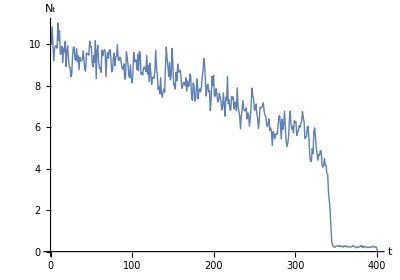

```mathematica
(* single realisation plot *)
plotSingleExp=ListLinePlot[expSeries[[1]],
ImageSize->400,
AspectRatio->0.7,
PlotStyle->Thickness[0.0025],
PlotRange->All,
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

### Simulate truncation scenario

```mathematica
(* set grazing rate and exploitation fate *)
f=0;
rVals=Subdivide[0.5,2.6,tmax];
```

```mathematica
For[i=1,i≤numSims,i++,
(* array for trajectory *)
x=ConstantArray[0,tmax+1];
(* set initial condition *)
x[[1]]=10;
(* normal random variables mean zero variance 1 for noise *)
noise=RandomVariate[NormalDistribution[0,1],tmax];
(* begin simulation *)
For[q=1,q≤tmax,q++,
r=rVals[[q]];
x[[q+1]]=fun[r,k,f,h,noise[[q]],x[[q]]];
(* don't let x go negative *)
If[x[[q+1]]<0,
x[[q+1]]==0;];
];
(* add trajectory to series array *)
trunSeries[[i,;;]]=x;
]
```

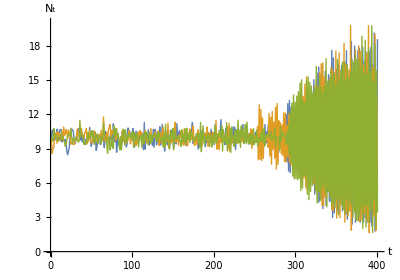

```mathematica
(* single realisation plot *)
plotSingleTrun=ListLinePlot[trunSeries[[1;;3]],
ImageSize->400,
AspectRatio->0.7,
PlotStyle->Thickness[0.0025],
PlotRange->{0,20},
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

## Exploitation scenario - traditional EWS

### Key values / parameters

```mathematica
(* control parameter range *)
fl=0;
fh=3;
(* saddle node bifurcation values *)
fcrit1=2.364; 
fcrit2=1.491;
(* transition time make prebifTime yrs less than bifurcation to account for noise *)
prebifTime=10;
tcritExp=Floor[(fcrit1-fl)*tmax /(fh-fl)]-prebifTime;



(* plot parameters *)
aHeadSize=0.03;
```

### Detrending Process (Gaussian Filter)

```mathematica
(* Detrend data up to transition *) 
tVals=Range[0,tmax];
dataFitExp=If[detrendOp==1,
Table[
GaussianFilter[expSeries[[i,1;;tcritExp]],tcritExp*bandWidth],
{i,1,numSims}],
ConstantArray[0,{numSims,tcritExp}]
];
```

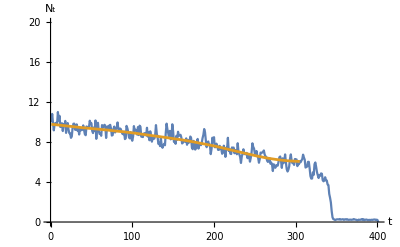

```mathematica
(* plot of single realisation *)
plotNum=1;
ListLinePlot[{expSeries[[plotNum]],dataFitExp[[plotNum]]},
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","N_t"},
PlotRange->{{0,tmax},{0,20}},
PlotStyle->{Default,Thickness[0.005]},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

```mathematica
(* compute residuals of series *)
residualsExp=expSeries[[1;;numSims,1;;tcritExp]]-dataFitExp;
residualsExp//Dimensions
```

{5,305}

### Variance

```mathematica
(* number of component in the rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];

(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
varSeriesExp=Table[MovingMap[Variance,residualsExp[[i]],windowComps],{i,1,numSims}];
varSeriesExp//Dimensions
```

{5,205}

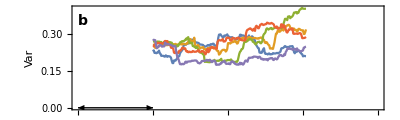

```mathematica
(* plot individual realisations *)
varPlotExp=ListPlot[Table[{tVals[[windowComps+1;;tcritExp]],varSeriesExp[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{{{0,0},{0.0005,0.5},{0.001,1},{0.0015,1.5}},Automatic},{Automatic,Automatic}},*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Coefficient of variation

```mathematica
(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
meanSeriesExp=Table[MovingMap[Mean,expSeries[[i,1;;tcritExp]],windowComps],{i,1,numSims}];
meanSeriesExp//Dimensions
```

{5,205}

```mathematica
cvSeriesExp=Table[Sqrt[varSeriesExp[[i]]]/meanSeriesExp[[i]],{i,1,numSims}];
cvSeriesExp//Dimensions
```

{5,205}

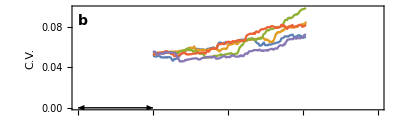

```mathematica
(* plot individual realisations *)
cvPlotExp=ListPlot[Table[{tVals[[windowComps+1;;tcritExp]],cvSeriesExp[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{{{0,0},{0.0005,0.5},{0.001,1},{0.0015,1.5}},Automatic},{Automatic,Automatic}},*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at lag 1

```mathematica
(* form [a1;a2;,,,;an] *)
acSeriesExp=Table[MovingMap[CorrelationFunction[#,1]&,residualsExp[[i]],windowComps],{i,1,numSims}];  
acSeriesExp//Dimensions
(* sim number,time value *)
```

{5,205}

```mathematica
tVals[[windowComps+1;;]]//Dimensions
```

{301}

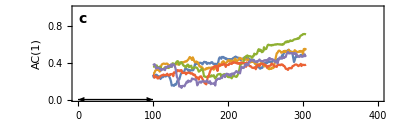

```mathematica
(* ac-1 plot of single realisations *)
acPlotExp=ListPlot[Table[{tVals[[windowComps+1;;tcritExp]],acSeriesExp[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC(1)",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{0,1}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0(* yorigin value *)}],Scaled[{0,arHeight},{windowComps,0 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

## Power Spectrum EWS

### Compute power spectrum over rolling window with same offset has Hamming windows

```mathematica
(* evaluate power spectrum of residuals in rolling window with the offset the same as hamOffset *)
pSpecSeriesExp=Table[MovingMap[TBPowerSpecWelch[{#,1,hamLength,hamOffset}]&,residualsExp[[i]],{windowComps,Left,hamOffset}],{i,1,numSims}];
```

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesExp[[1,1,1]];
```

```mathematica
pSpecSeriesExp//Dimensions
```

{5,41}

### Plot of individual realisations

```mathematica
(* plot times to use *)
plotTimes=Range[1*windowComps+hamOffset,tcritExp,hamOffset]
```

{105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305}

```mathematica
Length[plotTimes]
```

41

```mathematica
tcritExp
```

305

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

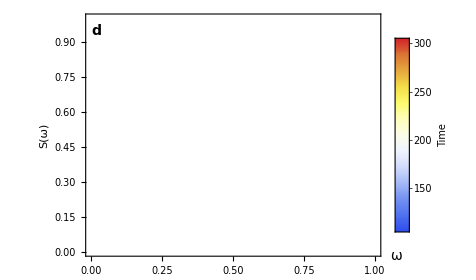

```mathematica
(* normalise to map to a colour *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
psdSinglePlotExp=ListLinePlot[Table[Transpose[pSpecSeriesExp[[4,tindex]]],{tindex,1,Length[plotTimes]}],
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{(*Text[Style["×10^-3",14],Scaled[{0.065,1.05}]],*)
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
(*FrameTicks->{{Transpose[{Range[0,5,0.5]*10^(-3),Range[0,5,0.5]}],Automatic},{Automatic,Automatic}},*)
PlotLegends->Placed[colLegend,Scaled[{0.9,0.55}]]]
```

### Max-frequency component

```mathematica
pSpecSeriesExp//Dimensions
```

{5,41}

```mathematica
(* Subscript[S, max] data *)
specMaxExp=Table[Max[pSpecSeriesExp[[i,j,2,;;]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesExp][[2]]}];
specMaxExp//Dimensions
```

Part::partw: Part 2 of TBPowerSpecWelch[{{0.206636,1.04688,0.165957,-0.583873,0.0341159,0.170197,0.185009,0.0735124,1.29497,«34»,0.162017,0.104595,0.122615,0.0836548,0.766581,0.500129,0.532181,«51»},1,10,5}] does not exist.

Part::partw: Part 2 of TBPowerSpecWelch[{{0.170197,0.185009,0.0735124,1.29497,0.465577,0.931192,-0.181022,-0.0981245,0.213415,«34»,0.500129,0.532181,-0.232203,-0.437894,0.119186,-0.205342,0.848913,«51»},1,10,5}] does not exist.

Part::partw: Part 2 of TBPowerSpecWelch[{{0.931192,-0.181022,-0.0981245,0.213415,-0.555644,0.144996,-0.0329173,0.488205,-0.703393,«34»,-0.205342,0.848913,-0.985037,0.367479,0.636392,-0.160564,-0.465203,«51»},1,10,5}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{5,41}

```mathematica
tVals[[windowComps+1;;tcritExp;;hamOffset]]//Dimensions
```

{41}

Part::partw: Part 2 of TBPowerSpecWelch[{{0.206636,1.04688,0.165957,-0.583873,0.0341159,0.170197,0.185009,0.0735124,1.29497,«34»,0.162017,0.104595,0.122615,0.0836548,0.766581,0.500129,0.532181,«51»},«6»,«7»,5.}] does not exist.

Part::partw: Part 2 of TBPowerSpecWelch[{{0.170197,0.185009,0.0735124,1.29497,0.465577,0.931192,-0.181022,-0.0981245,0.213415,«34»,0.500129,0.532181,-0.232203,-0.437894,0.119186,-0.205342,0.848913,«51»},«2»,5.}] does not exist.

Part::partw: Part 2 of TBPowerSpecWelch[{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

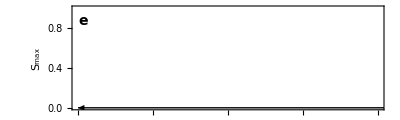

```mathematica
(* plot individual realisations *)
specMaxPlotExp=ListPlot[Table[{tVals[[windowComps+1;;tcritExp;;hamOffset]],specMaxExp[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{Transpose[{10^(-3)*Range[0,10],Range[0,10]}],Automatic},{Automatic,Automatic}},*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### Hopf-AIC weight

```mathematica
?TBHopfAIC
```

Information::notfound: Symbol TBHopfAIC not found.

```mathematica
pSpecSeriesExp//Dimensions
```

{5,41}

```mathematica
Timing[TBFitSpec[pSpecSeriesExp[[1,10]]]]
```

{0.000021,TBFitSpec[TBPowerSpecWelch[{{0.122615,0.0836548,0.766581,0.500129,0.532181,-0.232203,-0.437894,0.119186,-0.205342,0.848913,-0.985037,0.367479,0.636392,-0.160564,-0.465203,-0.401458,-0.632077,0.444177,0.184203,0.370791,0.501296,0.421376,-0.803791,0.134459,0.377788,0.117369,0.488598,0.554092,0.19574,-0.49902,-0.447436,0.174781,0.430548,-0.149872,0.247339,0.32693,0.875731,0.179724,0.134419,0.298041,0.240286,-0.0323167,-0.226572,-0.25369,0.0169509,-0.71453,-0.626054,0.626442,0.400266,0.0577415,-0.492758,-0.586246,0.0503649,-0.543741,-0.793681,-0.364888,0.696392,0.25151,0.349868,0.343139,-0.110737,0.659423,-0.132043,0.818084,0.726796,-0.258519,-0.173168,-0.276904,0.063243,0.139835,0.0391256,-0.054787,0.714693,-0.156064,0.266293,-0.499021,0.405016,-0.0711355,-0.607272,-0.253873,-0.237321,-0.271601,0.0931785,1.10385,0.251951,-0.0968636,-0.747591,-0.630584,-0.945117,-0.150338,-0.856506,-1.07481,-0.795559,-0.654977,-0.791729,0.480704,1.39784,0.83569,0.464527,0.0339993,0.720791},1,10,5}]]}

```mathematica
(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesExp=Monitor[
Table[Quiet[TBFitSpec[pSpecSeriesExp[[i,j]]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesExp]⟦2⟧}],
{ProgressIndicator[i,{1,numSims}],ProgressIndicator[j,{1,Dimensions[pSpecSeriesExp]⟦2⟧}]}];
```

```mathematica
aicWeightSeriesExp//Dimensions
```

{5,41}

```mathematica
(* plot of individual realisations for wfold *)
aicFoldPlotExp=ListPlot[Table[
{tVals[[windowComps+1;;tcritExp;;hamOffset]],aicWeightSeriesExp[[i,;;,1]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
PlotStyle->TMBcolours[[1]],
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameLabel->{{"w_fold",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}];
```

```mathematica
(* plot of individual realisations for whopf *)
aicHopfPlotExp=ListPlot[Table[
{tVals[[windowComps+1;;tcritExp;;hamOffset]],aicWeightSeriesExp[[i,;;,2]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotStyle->TMBcolours[[4]],
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{False,True},{False,False}},
FrameStyle->{Automatic,Automatic,Automatic,TMBcolours[[4]]},
FrameLabel->{{"","w_hopf"},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{None,Range[0,1,0.2]},{None,None}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3];
```

Part::partw: Part 2 of TBFitSpec[TBPowerSpecWelch[{{0.206636,1.04688,0.165957,-0.583873,0.0341159,0.170197,0.185009,0.0735124,«35»,0.162017,0.104595,0.122615,0.0836548,0.766581,0.500129,0.532181,«51»},1,10,5}]] does not exist.

Transpose::nmtx: The first two levels of {{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300},«1»} cannot be transposed.

Part::partw: Part 2 of TBFitSpec[TBPowerSpecWelch[{{0.128206,-0.276366,1.27229,0.0323546,0.263924,-0.355669,0.332829,0.425846,«35»,0.21362,-0.588732,0.569523,0.233536,-0.311731,-0.0550798,0.0687267,«51»},1,10,5}]] does not exist.

Transpose::nmtx: The first two levels of {{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300},«1»} cannot be transposed.

Part::partw: Part 2 of TBFitSpec[TBPowerSpecWelch[{{0.0508807,-0.0529095,-0.140721,0.97746,0.283053,0.655626,0.41474,0.0791168,«35»,0.289675,1.02103,0.299104,0.476567,1.15257,1.12926,0.089224,«51»},1,10,5}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

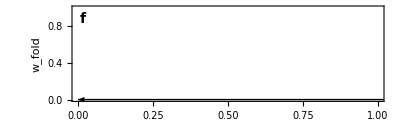
-Graphics--Graphics-

```mathematica
aicPlotExp=Overlay[{aicFoldPlotExp,aicHopfPlotExp}]
```

## Bifurcation Diagram (exploited pop)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/fisheries/bifurcation/fish_exp.dat"];
```

```mathematica
(* Import data *)
rawdata=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/fisheries/bifurcation/fish_exp.dat"];

(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
fbifVals=fulldata[[;;,1]];
tbifVals=(fbifVals-fl)*tmax /(fh-fl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections[[3]]=Cases[nodeSections[[3]],{x_,_,_,_}/; x>0] ; 
nodeSections=Append[nodeSections,Cases[nodeSections[[6]],{_,x_,_,_}/;x>0]];
nodeSections[[6]]=Cases[nodeSections[[6]],{_,x_,_,_}/;x<0]; *)(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

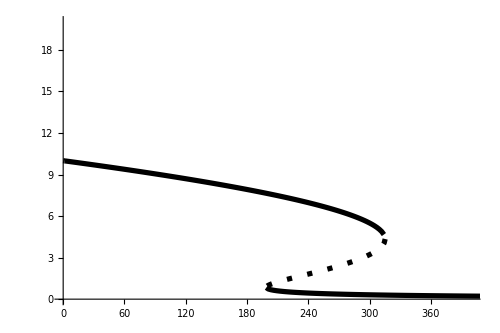

```mathematica
(* Make plot *)
bifPlotExp=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

```mathematica
plotSingleExp
```

-Graphics-

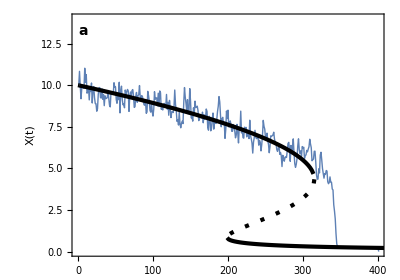

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajX=Show[{plotSingleExp,bifPlotExp},
PlotRange->{{0,tmax},{0,14}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
]
```

## Combined Plot

```mathematica
ewsPlot=Grid[{{bifTrajX,psdSinglePlotExp},{varPlotExp,specMaxPlotExp},{acPlotExp,aicPlotExp}},Spacings->{-2.5,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
Export["figures/ews_ricker_single_exp.png",ewsPlot,ImageResolution->200];
```